```mathematica
f[p_]={p*1000+(1-p)*1001000,p*1000000 + (1-p)*0};
f[.6]
```

{401000.,600000.}

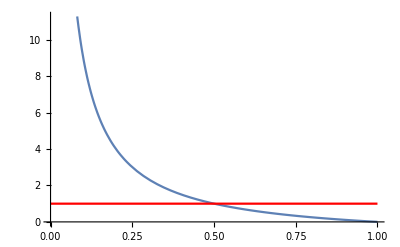

```mathematica
g[p_] = (p*1000+(1-p)*1001000)/(p*1000000 + (1-p)*0);
Show[Plot[g[p],{p,0,1}],Plot[1,{x,0,1},PlotStyle->Red]]
```

```mathematica
f[.5005]
```

{500500.,500500.}

```mathematica
Integrate[p*1000+(1-p)*1001000,{p,0,1}]
```

501000

```mathematica
Integrate[p*1000000 + (1-p)*0,{p,0,1}]
```

500000

```mathematica
f[.5005]
```

{500500.,500500.}

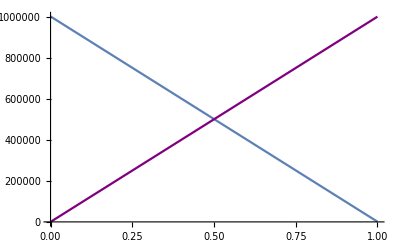

```mathematica
Show[Plot[p*1000+(1-p)*1001000,{p,0,1}],Plot[p*1000000 + (1-p)*0,{p,0,1},PlotStyle->Purple]]
```